# Line search: Visualizing the Wolfe Conditions

We know much less about any realistic function than we think. We have no contour plot or anything remotely equivalent! We are at  point x_k and our target is to efficiently find a better point x_(k+1)=x_k+α_k p_k using only local information.

```mathematica
Clear[f,df,x,y]
f[{x_,y_}]:= Sin[2 x + Cos[3x-y^2]]+x Sin[ y Cos[2x-ArcTan[x+3y]]]+0.2(x^2+y^2)
df[{x_,y_}]=D[f[{x,y}],{{x,y}}];
ddf[{x_,y_}]=D[f[{x,y}],{{x,y},2}];
CPic=ContourPlot[f[{x,y}],{x,-5,5},{y,-5,5},Contours->20]
```

-Graphics-

## Directions: p_k

The first thing to do is find a descent direction. We should be able to do better than trying random directions.  There are three strategies:
Steepest descent 
	p_SD=-df[x_k];
Newton 
	p_N=-ddf[x_k]^-1.df[x_k];
and Quasi-Newton defined by an updated approximation B_k≈ddf[x_k]
	p_QN=-B_k^-1.df[x_k].
	
p_SD is always a descent direction. 
p_N is a descent direction if the Hessian ddf[x_k] is positive definite. 
P_QNis a descent direction if we choose B_k to be positive definite.

```mathematica
Clear[mk,xk]
xk={1.2,2.3};
pSD=-df[xk];
pN=-LinearSolve[ddf[xk],df[xk]];
mk[{x_,y_}]= f[xk]+df[xk].({x,y}-xk)+0.5 ({x,y}-xk).ddf[xk].({x,y}-xk);
TabView[{
"Big Picture"->Show[CPic,
Epilog->{
{Red,Arrow[{xk,xk+ pSD}]},
{Cyan,Arrow[{xk,xk+ pN}]},
{Green,Point[xk]}
},
PlotLabel->Eigenvalues[ddf[xk]]],
"Close Up"->Show[
ContourPlot[mk[{x,y}],
{x,y}∈Disk[xk,1.5 Norm[pN]],PlotLegends->Automatic,
Contours->20,ContourStyle->Blue],
ContourPlot[f[{x,y}],
{x,y}∈Disk[xk,1.5 Norm[pN]],PlotLegends->Automatic,
Contours->20,ContourShading->None,ContourStyle->Green],
Epilog->{
{Red,Arrow[{xk,xk+ pSD}]},
{Cyan,Arrow[{xk,xk+ pN}]},
{Green,Point[xk]}
}]
}]
```

12

```mathematica
Clear[mk,xk]
xk={1.5,-1.3};
pSD=-df[xk];
pN=-LinearSolve[ddf[xk],df[xk]];
mk[{x_,y_}]= f[xk]+df[xk].({x,y}-xk)+0.5 ({x,y}-xk).ddf[xk].({x,y}-xk);
TabView[{
"Big Picture"->Show[CPic,
Epilog->{
{Red,Arrow[{xk,xk+ pSD}]},
{Cyan,Arrow[{xk,xk+ pN}]},
{Green,Point[xk]}
},
PlotLabel->Eigenvalues[ddf[xk]]],
"Close Up"->Show[
ContourPlot[mk[{x,y}],
{x,y}∈Disk[xk,1.5 Norm[pN]],PlotLegends->Automatic,
Contours->20,ContourStyle->Blue],
ContourPlot[f[{x,y}],
{x,y}∈Disk[xk,1.5 Norm[pN]],PlotLegends->Automatic,
Contours->20,ContourShading->None,ContourStyle->Green],
Epilog->{
{Red,Arrow[{xk,xk+ pSD}]},
{Cyan,Arrow[{xk,xk+ pN}]},
{Green,Point[xk]}
}]
}]
```

12

If the Hessian is positive definite the critical point minimizes the quadratic approximation. In this case it makes sense to use the critical point. If the Hessian is not positive definite the critical point does not minimize the quadratic approximation. In this case it does not make sense to use the critical point. The Quasi-Newton idea is that fixing bits of the curvature is useful.

## Step size α_k

For line search need to find OK step lengths with very limited information.

```mathematica
xk={1.7,1.3};
pk=-{-1.2,-1.6};
{c1,c2}={0.5,0.7};
TabView[{
"BigPic"->Show[ CPic,
Epilog->{
{Red,Arrow[{xk,xk+ pk}]},
{Green,Point[xk]}}],
"Line Search"->Show[
Plot[f[xk+α pk],{α,0, 2},PlotStyle->Directive[Green,Thick],
RegionFunction->Function[α,df[xk+α pk].pk>c2*df[xk].pk]],
Plot[f[xk+α pk],{α,0, 2},PlotStyle->Directive[Red,Dashed],
RegionFunction->Function[α,f[xk+α pk]<f[xk]+c1 α df[xk].pk]],
Plot[f[xk+α pk],{α,0, 2},PlotStyle->Dotted],
PlotLabel->StringForm["c_1=`` and c_2=``",c1,c2],
Epilog->{Thin,Pink,Line[{{0,f[xk]},{2,f[xk]+c1*2*df[xk].pk}}]}
]
},2]
```

12

The first test (in pink) makes sure that the step is making some fraction of the progress (descent) that the gradient says it should be able to make in the direction p_k in practice 0<c_1<1 is small.  A common default is 10^-4. In practice, if you fail this test with some value of α you should decrease the value of α.

The second test (in green) makes sure that the step winds up at a flatter (or uphill) portion of the graph of f[x_k+α p_k].  In practice 0<c_2<1 is not small.  A common default is 0.9. In practice, if you fail this test you should increase the value of α.

You can prove that there is always a point satisfying both Wolfe conditions provided 0<c_1<c_2<1. Common default values are {c_1,c_2}≈{10^-4,0.9} for most line search methods and {c_1,c_2}≈{10^-4,0.1} when it is important to make sure that the end of the step is reasonably flat.

Wolfe One is also called the Armijo condition.  Wolfe Two is also called the curvature condition.

## Step Size adjustment

We need to adjust step lengths with very limited information.

Some code only enforces the Wolfe One condition. The step size control is rudimentary. Always start from some maximum step size and multiply by some constant less than one (a common value is 0.5) if you fail the Wolfe One condition! This is called BackTracking. This sort of step size control does not need the gradient.

Most code enforces both Wolfe conditions and use gradient information. After a trial step α_k you have the value and slope at α=0 and the value and slope at α=α_k.  There is a unique cubic Hermite interpolant that matches these values and slopes with an interior critical point which is a minimum if p_k is a descent direction and the terminal slope is positive. The more-sophisticated step size tries the step size that worked for the previous step then multiplies the step size by a constant (a common value is 2) greater than one if the Wolfe tests indicate increased step size and interpolate to the Hermite critical point to decrease the step size.

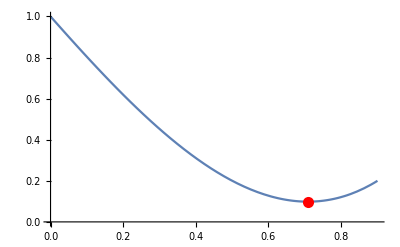

```mathematica
{f0,s0}={1,-2};
{αk,fαk,sαk}={0.9,0.2,1.1};
h=Interpolation[{{{0},f0,s0},{{αk},fαk,sαk}}];
Quiet[cp=α/.Solve[h'[α]==0,α]⟦1⟧];
Plot[h[α],{α,0,αk},
Epilog->{Red,PointSize[0.02],Point[{cp,h[cp]}]}]
```

Our book gives formulae and pseudo-code for all of this and proves that all the pieces fits together to reliably give reasonable values for the step length.